```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mjhug\Dropbox (Personal)\Amateur Radio\FT8

```mathematica
(* FT8 Time Syncronization *)
```

```mathematica
TableForm[Transpose@(costasArray={{0,3},{1,1},{2,4},{3,0},{4,6},{5,5},{6,2}})]
gridSize=7
```

0 | 1 | 2 | 3 | 4 | 5 | 6
3 | 1 | 4 | 0 | 6 | 5 | 2

7

```mathematica
(*Create an empty grid*)
TableForm[grid=ConstantArray[0,{gridSize,gridSize}]]

(*Populate the grid based on the Costas array*)
Do[
(*Adjust the indices to fit within the grid dimensions*)grid[[costasArray[[i+1,2]]+1,i+1]]=i+1,{i,0,Length[costasArray]-1}]
TableForm[grid]
```

0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0

0 | 0 | 0 | 4 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0

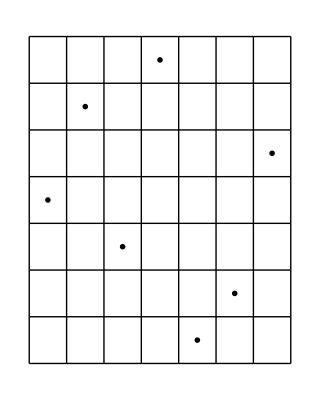

```mathematica
(* Static Grid Visualization *)
GraphicsGrid[Map[If[#==0,"",Graphics[{Red,Rectangle[],Text[Style[#,Bold, Black, FontFamily->"Belgium"],{0.5,0.5}]}]]&,grid,{2}],Frame->All]
```

```mathematica
(*Looks like the origin is the top left corner instead of bottom left.  Ah well.  Just an explainer.*)
```

```mathematica
(*Parameters*)rows=7;
cols=33;
costasSize=7;
costasArray={{0,3},{1,1},{2,4},{3,0},{4,6},{5,5},{6,2}};
frameRate=20; (*Frames per transition for smooth movement -- haven't finished this part yet*)

(*Create a background grid with random 0s and 1s*)
backgroundGrid=RandomChoice[{1,6}->{0,1},{rows,cols}]

(*Choose a random position for the Costas array to match and ensure a match exists*)
matchRow=RandomInteger[{1,rows-costasSize+1}];
matchCol=RandomInteger[{1,cols-costasSize+1}];
Do[backgroundGrid[[matchRow+costasArray[[i,2]],matchCol+i]]=0,{i,Length[costasArray]}];

(*Function to overlay the Costas array on the background grid*)
overlayCostas[grid_,row_,col_]:=Module[{overlayedGrid=grid},Do[With[{r=Ceiling[row]+costasArray[[i,2]],c=Ceiling[col]+i},If[1<=r<=rows&&1<=c<=cols,overlayedGrid[[r,c]]=2]],{i,Length[costasArray]}];
overlayedGrid];

(*Function to create a frame of the animation*)
createFrame[grid_,row_,col_,matchFound_]:=Graphics[Table[If[grid[[r,c]]==2,If[matchFound,{Green,Rectangle[{c,-r}]},{Red,Rectangle[{c,-r}]}],If[grid[[r,c]]==1,{White,Rectangle[{c,-r}]},{Black,Rectangle[{c,-r}]}]],{r,rows},{c,cols}],Frame->False,ImageSize->{cols*20,rows*20}];

(*Generate frames for the animation*)
foundMatch=False;
frames={};

Do[(*Check for match*)If[matchesAtPosition[backgroundGrid,Ceiling[row],Ceiling[col]],foundMatch=True;
AppendTo[frames,createFrame[overlayCostas[backgroundGrid,row,col],row,col,True]];
Break[];];
(*Add frame for current position*)AppendTo[frames,createFrame[overlayCostas[backgroundGrid,row,col],row,col,False]];
(*If next position is the match position,interpolate smoothly*)If[row<matchRow&&col<matchCol,Do[AppendTo[frames,createFrame[overlayCostas[backgroundGrid,row+i/frameRate,col+i/frameRate],row+i/frameRate,col+i/frameRate,False]],{i,1,frameRate-1}]],{row,1,rows-costasSize+1,1},{col,1,cols-costasSize+1,1}];

ListAnimate[Flatten@frames]
Length[frames]
```

{{1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,0,1,1,1},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1},{1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1},{1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1}}

21

```mathematica
Export["Hughes_CostasArrayMatchAgainstRandomArray.gif",frames,"DisplayDurations"->Flatten[{Table[0.05,Length[frames]-1],4}]]
```

Hughes_CostasArrayMatchAgainstRandomArray.gif

```mathematica
(* Be cooler if it was sound.  But I don't know how to put that on our webpage. *)
```

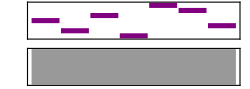

```mathematica
Sound[SoundNote[#]&/@{3,1,4,0,6,5,2}]
```

```mathematica
Export["CostasAudioSample.mp3",Sound[{SoundNote[3],SoundNote[1],SoundNote[4],SoundNote[0],SoundNote[6],SoundNote[5],SoundNote[2]}]]
```

CostasAudioSample.mp3